LAB O2: Variation of Atmospheric Pressure with Altitude

Part 1: Calibration of the pressure transducer
Introduction
The calibration constant C of the pressure transucer would be determined in this part of the experiment.

```mathematica
VccF= 1189; (*Volume of the flask (cc)*)
δVccF=7;(*error of volume of flask (cc)*)
VccH=40; (*volume of the hose(cc)*)
δVccH= 1;(*Error of volume of hose (cc)*)
VccS=30;(*Starting volume of the syringe(cc)*)
δVccS=1;(*error of starting volume of syringe (cc)*)
V=VccF+VccH+VccS; (*Total volume of the system (cc)*)
δV=√((δVccF)^2+(δVccH)^2+(δVccS)^2);(*error of the total volume (cc)*)
VC={15,10,5,-5,-10,-15};(*Change in volume (cc)*)
P=625; (*Starting atmospheric pressure (torr)*)
Vin=0.06;(*Initial voltage (volts)*)
Vcal={-0.677,-0.460,-0.205,0.301,0.537,0.785};(*calculated voltage (volts)*)
Volt=Vcal-Vin; (*The change in voltage (volts)*)
δVolt=0.001;(*error in calculated voltage (volts)*)
VCvsVolt= Thread[{VC,Volt}];
Grid[Prepend[VCvsVolt,{"Change in volume (cc)", "voltage Reading (volts)"}], Frame -> All]
```

Change in volume (cc) | voltage Reading (volts)
15 | -0.737
10 | -0.52
5 | -0.265
-5 | 0.241
-10 | 0.477
-15 | 0.725

Part 2: Change of Pressure with Temperature
Introduction
The main goal for this part of the lab was to determine the effect of the temperature on the pressure of the system. We first allowed the system to reach equilibrium by opening the system from one end. We later warmed the flask with our bear hands for about 20 seconds, hence, warming the air inside the system. This also increased the pressure in the system because of the air expanding due to it being warmer than it was at equilibrium. Thus, the change in voltage to determin ehte effects of the termperature on the system could be calculated.

```mathematica
Ivolt= 0.085; (*Initial voltage measured (volts)*)
Fvolt=0.150; (*Final voltage measured (volts)*)
Cvolt= Fvolt-Ivolt; (*Change in voltage (volts)*)
IniT=21+274.15;(*Initial temperature (kelvin)*)
T=20; (*duration of continous heating the flask (s)*)
```

Part 3: Change of Pressure with Temperature
Introduction
The main goal of this part was to determine how the change in altitude would effect the pressure inside the system. The system was closed and before entering the elevator the voltage reading was noted down. The system then was taken to the 10th floor of the Gamow Tower and then measured the reading again. Then the two measurements were used to determine the effect that a change in altitude has on air pressure.

```mathematica
Ivolt2=-0.026; (*Initial voltage (volts)*)
volt10=-0.295;(*voltage at the 10th floor (volts)*)
Fvolt2=-0.040;(*Final voltage reading at ground floor (volts)*)
CH=32.2;(*Change in height (m)*)
```

## Data analysis

Part 1: Calibration of the pressure transducer

Change in Pressure (torr | Change in Voltage (volts)
-7.44639 | -0.737
-4.96426 | -0.52
-2.48213 | -0.265
2.48213 | 0.241
4.96426 | 0.477
7.44639 | 0.725

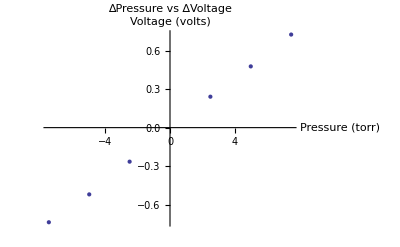

9.99904

0.435053

0.17761

```mathematica
PC=(-VC/V)*P//N; (*Change in pressure (torr)*)
PvsVolt=Thread [{PC, Volt}];
Grid[Prepend[PvsVolt,{"Change in Pressure (torr", "Change in Voltage (volts)"}], Frame-> All]
ListPlot[{PvsVolt}, PlotLabel-> "∆Pressure vs ∆Voltage", AxesLabel->{"Pressure (torr)", "Voltage (volts)"}]
CaliC=PC/Volt; (*Calculate values for the Calibration Constant C (torr/Volts)*)
CaliCAvg=(∑_(i=1)^6 CaliC[[i]])/6(*Avg Calibration Constant values (torr/volts)*)
StanDev= √((∑_(i=1)^6 (CaliC[[i]]-CaliCAvg)^2)/(6-1))(*Standard Diviation of Calibration Constant*)
StanDevM=StanDev/(√6)(*mean standard deviation*)
```

Due to all the caluclations, we calculated the average calibration constant which is extremely close to 10, which falls in the acceptable range of 10-12. Also, the standard deviation was calculated and it related to the data.

Part 2: Change of Pressure with Temperature

```mathematica
PC2=CaliCAvg *Cvolt (*Change in pressure (torr)*)
TC=PC2/P*IniT (*Temperature Change (Kelvins)*)
```

0.649938

0.306926

The temperature change was minimal due to it only having 0.306926 change in Kelvin. Similary with the change in pressure was minimal.

Part 3: Change of Pressure with Altitude

```mathematica
VC2=volt10-Ivolt2; (*Change in voltage from the basement to the 10th floor (volts)*)
VC3= volt10-Fvolt2; (*change in voltage from the 10th floor and then back to the basement (volts)*)
AvgVC= (VC2+VC3)/2;(*Avg voltage change between the basement and the 10th floor (volts)*)
PC3= AvgVC*CaliCAvg (*Change in pressure (torr)*)
δP=0.001; (*uncertainity of pressure (torr)*)
SH=-P*CH/PC3(*calculation of scale height (m)*)
δH=P*(CH/((Log[((P+PC3)/P)])^2*(P+PC3)))*δP
```

-2.61975

7682.04

1832.73

## Conclusion

Part 1: Calibration of the pressure transducer
In the first part of this lab experiment, the purpose was to calculate the calibration constant. In conclusion, we calculated the final average calibration constant to be 9.99~10 torr/volts, which falls into the acceptable calibration constant values between 10-12 torr/volts. Then, the standard deviation was calculated to develop a statistical measure of the mean variance. Both values were acceptable and were around the expected values. To obtain more of a precise value of the calibration constant or more between the range of 10-12, a system should be used in which the temperature is controlled and the the temperature of the hand affecting the air particles to be measured. 


Part 2: Change of Pressure with Temperature
In the second part of this lab experiment, the purpose was to determine the effect of temperature on the pressure inside the system. In conclusion, we calculated the Pressure change and the Temperature change due to heating up the air particles inside the system over a period of 20 seconds with our hands and we had a minimal change in pressure and temperature. These were the following values respectively, 0.65 torr and 0.31 kelvin. Obviously there was a minimal change, in order to get a more precise idea of how much the temperature affects the pressure, we should’ve done more trials. As in, measure the temperature on the hands, place them over the system for 10s, then 20s, then 30s, then 40s, etc. Hence, giving valuable data and increasing the certainity of the calculations done post lab. 

Part 3: Change of Pressure with Altitude
In the third and final part of this lab experiment, the purpose was to determine the effect that the altitude has on the pressure inside the system. In conclusion, we calculated the average voltage change between 1) starting from the bottom and going to the 10th floor, and 2) starting from the 10th floor to the bottom; this was done because in both times that the voltage was measured at the basement, beginning and final, the voltage was off by 0.16 volts (which was still acceptable). This allowed us to calculate the pressure change with respect to altitude, giving us a pressure change of -2.62 torr. Hence, this allowed us to calculate the scale height, 7700m, and the uncertainity of the scale height, 1800m. We had a huge uncertainity regarding the scaler height however the litrature value for Earth is 8.5km of scale height, thus having our answer within the error and within the acceptable values. The error in this part can be caused by the temperature change within the system during the elevator ride up and down the tower, which could also be a factor since there were 4 people crowded in one tiny elevator going up.